## Mathematische Kalibrierung über 4 Messpunkte

Annahme: Zwei gemessene Verzerrungsfaktoren a und b sind linear voneinander abhängig als Gerade v. Indefinitdesimale Stecken multipliziert mit den Verzerrungsfaktoren ergeben eine um das Integral von v verzerrte Strecke.

#### Beamer X → Kamera X

Integriere über die Verzerrungsfunktion v(x) = a(1-x)+b x
a und b sind Verzerrungsfaktoren zwischen den zwei Vierecken (projziert und gemessen)

```mathematica
BeamerXZuKameraX[xb_,a_,b_]:=

1/2(b-a)xb^2+a xb; 

(*Integrate[a(1-x)+b x,{x,0,xb}]*)
```

#### Beamer Y → Kamera Y

Diese Funktion beschreibt einen linearen Ansatz für y. yk0 beschreibt den Offset zwischen linker und rechter Bildlinie.

```mathematica
BeamerYZuKameraY[xb_,yb_,a_,b_,yk0_]:=

(a yb+yk0)(1-xb)+b yb xb;
```

#### Kamera X → Beamer X

Mathematische Umkehrfunktion der Abbildung Beamer X → Kamera X

```mathematica
KameraXZuBeamerX[xk_,a_,b_]:=

(-a+√(a^2+2(b-a)xk))/(b-a) ;
```

#### Kamera Y → Beamer Y

Mathematische Umkehrfunktion der Abbildung Beamer Y → Kamera Y

```mathematica
KameraYZuBeamerY[yk_,xb_,a_,b_,yk0_]:=

(*(yk-yk0-yk0 xb)/(a-xb+b xb);*)
(yk-yk0+yk0 xb)/(a-a xb+b xb)
```

#### Baryzentrische ....

```mathematica
KameraPixel[paar_]:=
(1-x)*(1-y)*{265.556,70.}+
(1-x)*y*{522.222,126.66699999999997}+
x*(1-y)*{265.556,313.33299999999997}+
x*y*{533.333,333.33299999999997}/.{x->paar[[1]],y->paar[[2]]};
```

#### Vergleichsplot

Diese Funktion nimmt Paare von Beamerpunkten und Kamerapunkten entgegen in der Form {{{x_b,y_b},{x_k,y_k}},..}
Die Ausgabe sind zwei Plots. Der erste vergleicht die gemessenen Kamerapunkte mit den berechneten. Der zweite Plot vergleicht die berechneten Beamerpunkte mit den projzierten.

```mathematica
VergleichsPlot[paare_,eckpunktpaare_]:=Module[
{beamerPoints,cameraPoints,LU,LL,RU,RL,xkOffset,ykLeftOffset,ykRightOffset,a,b,xk,yk,xb,yb, beamerResults,stauchung},

beamerPoints=Flatten[Take[paare,All,1],1];
cameraPoints=Flatten[ Take[paare,All,-1],1];

LU=eckpunktpaare[[1]];
LL=eckpunktpaare[[2]];
RU=eckpunktpaare[[3]];
RL=eckpunktpaare[[4]];

Print["LU: ",LU, "\nLL: ",LL, "\nRU: ",RU,"\nRL: ", RL];

xkOffset=Mean[{LU[[2,1]],LL[[2,1]]}]//N; (*Screen Left X*)
ykLeftOffset=LU[[2,2]]; (*Screen Top Y*)
ykRightOffset=RU[[2,2]]; (*Screen Bottom Y*)

a=EuclideanDistance[LU[[2]],LL[[2]]]/EuclideanDistance[LU[[1]],LL[[1]]]//N;
b=EuclideanDistance[RU[[2]],RL[[2]]]/EuclideanDistance[RU[[1]],RL[[1]]]//N;
maxDist=Mean[{RU[[2,1]],RL[[2,1]]}]-xkOffset;
maxVal=BeamerXZuKameraX[1,a,b];
stauchung=maxDist/maxVal;

(*
Print["a: ",  a,"\nb: ",b];
Print["Screen Offset xk: ",xkOffset];
Print["Screen Width: ",maxDist];
Print["Overflow: ",maxVal];
Print["Stauchung: ",stauchung];

Print["Offset yk Left: ",ykLeftOffset];
Print["Offset yk Right: ",ykRightOffset];
*)

(* Calculate Beamer -> Camera Coordinates *)
cameraResults={};
cameraBary={};
For[i=1,i<Length[beamerPoints]+1,i++,
xb=beamerPoints[[i,1]];
yb=beamerPoints[[i,2]];
xk=BeamerXZuKameraX[xb,a,b]*stauchung+xkOffset;
yk=BeamerYZuKameraY[xb,yb,a,b,ykLeftOffset-ykRightOffset]+ykRightOffset;
cameraResults=Append[cameraResults,{xk,yk}];
];
For[i=1,i<Length[cameraResults]+1,i++,
yh=x/.Simplify[Solve[Det[
{
(1-x)cameraResults[[1]]+x*cameraResults[[5]]-cameraResults[[i]],(1-x)*cameraResults[[21]]+x*cameraResults[[25]]-cameraResults[[i]]
}
]==0,x]][[1]];
xh=y/.Simplify[Solve[Det[{(1-y)cameraResults[[1]]+y*cameraResults[[21]]-cameraResults[[i]],(1-y)*cameraResults[[5]]+y*cameraResults[[25]]-cameraResults[[i]]}]==0,y]][[1]];
cameraBary=Append[cameraBary,KameraPixel[{xh,yh}]];
];


Print[ListPlot[{cameraPoints,cameraResults,cameraBary},
PlotStyle->{{Green, PointSize[Large]},{Red,PointSize[Large]},{Blue,PointSize[Large]}},
PlotLegends->{"Gemessen","Berechnet", "Baryzentrisch"}]];

(* Calculate Camera -> Beamer Coordinates *)
beamerResults={};
For[i=1,i<Length[cameraPoints]+1,i++,
xk=cameraPoints[[i,1]];
yk=cameraPoints[[i,2]];
xb=KameraXZuBeamerX[xk-xkOffset,a,b](*/stauchung*);
yb=KameraYZuBeamerY[yk-ykRightOffset,xb,a,b,ykLeftOffset-ykRightOffset];
beamerResults=Append[beamerResults,{xb,yb}];
];

Print[ListPlot[{beamerPoints,beamerResults},
PlotStyle->{{Green, PointSize[Large]},{Red,PointSize[Large]}},
PlotLegends->{"Projziert","Berechnet"}]];
];
```

### Test an Bild 1 (1:1 → 1296:968) - gross links zu klein rechts

Aufnahme mit iPhone 4. 
-Graphics-
Bemerkung: x und y wurden vertauscht.

```mathematica
paare={
{{0,0},{467,148}},
{{0,1},{460,480}},
{{1,0},{737,195}},
{{1,1},{732,488}},
{{.5,.5},{611,328}}
};

a1=EuclideanDistance[paare[[1,2]],paare[[2,2]]]/
EuclideanDistance[paare[[1,1]],paare[[2,1]]]//N
b1=EuclideanDistance[paare[[3,2]],paare[[4,2]]]/
EuclideanDistance[paare[[3,1]],paare[[4,1]]]//N
(*a=(paare[[1,2,2]]-paare[[2,2,2]])/
(paare[[1,1,2]]-paare[[2,1,2]])//Abs//N
b=(paare[[3,2,2]]-paare[[4,2,2]])/
(paare[[3,1,2]]-paare[[4,1,2]])//Abs//N*)
```

332.074

293.043

Test mit Stauchung und Offset:

```mathematica
max=BeamerXZuKameraX[1,a1,b1]
BeamerXZuKameraX[.5,a1,b1]/max*(734-463)+463
```

312.558

602.73

Input xb, yb, a, b, y-Offset zwischen links und rechts

```mathematica
yk=BeamerYZuKameraY[0,1,a1,b1,-48]+195
```

479.074

```mathematica
yk-195
KameraYZuBeamerY[%,0,a1,b1,-48]
```

284.074

1.

LU: {{0,0},{467,148}}
LL: {{0,1},{460,480}}
RU: {{1,0},{737,195}}
RL: {{1,1},{732,488}}

Part::partw: Part 21 of {{463.5, 148.}, {463.5, 480.074}, {734.5, 195.}, {734.5, 488.043}, {603.23, 327.779}} does not exist.

Part::partw: Part 25 of {{463.5, 148.}, {463.5, 480.074}, {734.5, 195.}, {734.5, 488.043}, {603.23, 327.779}} does not exist.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 21 of {{463.5, 148.}, {463.5, 480.074}, {734.5, 195.}, {734.5, 488.043}, {603.23, 327.779}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

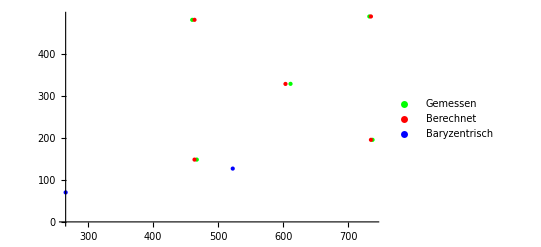

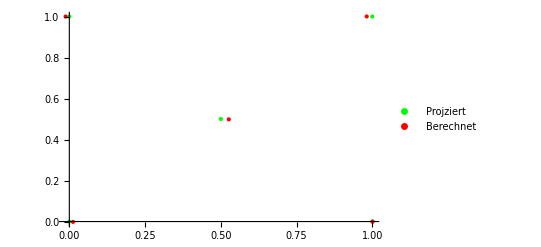

```mathematica
VergleichsPlot[paare,Take[paare,4]]
```

### Test an Bild 2 (1:1 → 640:478) - klein links zu gross rechts

Aufnahme mit iPhone 4. 
-Graphics-
Bemerkung: x und y wurden vertauscht

```mathematica
paare={
{{0,0},{234,118}},
{{0,1},{235,236}},
{{1,0},{310,100}},
{{1,1},{311,238}},
{{.5,.5},{268,174}}
};

a2=EuclideanDistance[paare[[1,2]],paare[[2,2]]]/
EuclideanDistance[paare[[1,1]],paare[[2,1]]]//N
b2=EuclideanDistance[paare[[3,2]],paare[[4,2]]]/
EuclideanDistance[paare[[3,1]],paare[[4,1]]]//N
```

118.004

138.004

Test mit Stauchung und Offset:

```mathematica
max=BeamerXZuKameraX[1,a2,b2]
BeamerXZuKameraX[.5,a2,b2]/max*(310.5-234.5)+234.5
```

128.004

271.016

```mathematica
BeamerYZuKameraY[.5,.5,a2,b2,18]+100
```

173.002

LU: {{0,0},{234,118}}
LL: {{0,1},{235,236}}
RU: {{1,0},{310,100}}
RL: {{1,1},{311,238}}

Part::partw: Part 21 of {{234.5, 118.}, {234.5, 236.004}, {310.5, 100.}, {310.5, 238.004}, {271.016, 173.002}} does not exist.

Part::partw: Part 25 of {{234.5, 118.}, {234.5, 236.004}, {310.5, 100.}, {310.5, 238.004}, {271.016, 173.002}} does not exist.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 21 of {{234.5, 118.}, {234.5, 236.004}, {310.5, 100.}, {310.5, 238.004}, {271.016, 173.002}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

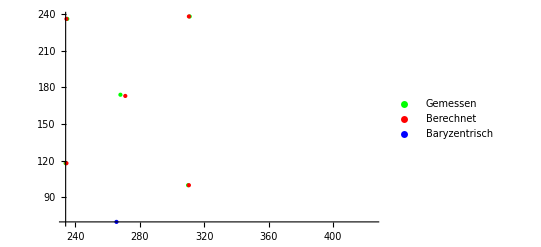

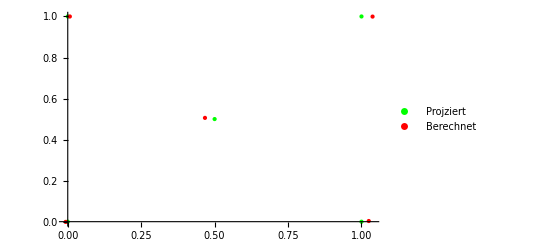

```mathematica
VergleichsPlot[paare,Take[paare,4]]
```

### Test an Bild 3 (1024:768 → 640:480)

Aufnahme mit T430s Integrated Webcam. Sie besteht aus 4x4 Quadranten. 
-Graphics-

```mathematica
paare={
{{0,0},{265.556,480-410.}},
{{.25,0},{337.778,480-393.333}},
{{.50,0},{404.444,480-378.889}},
{{.75,0},{465.556,480-365.556}},
{{1,0},{522.222,480-353.333}},

{{0,.25},{265.556,480-352.222}},
{{.25,.25},{340.,480-337.778}},
{{.50,.25},{406.667,480-324.444}},
{{.75,.25},{467.778,480-314.444}},
{{1,.25},{524.444,480-303.333}},

{{0,.50},{265.556,480-291.111}},
{{.25,.50},{341.111,480-280.}},
{{.50,.50},{408.889,480-270.}},
{{.75,.50},{470.,480-261.111}},
{{1,.50},{527.778,480-253.333}},

{{0,.75},{265.556,480-230.}},
{{.25,.75},{342.222,480-221.111}},
{{.50,.75},{410.,480-213.333}},
{{.75,.75},{472.222,480-206.667}},
{{1,.75},{530.,480-201.111}},

{{0,1},{265.556,480-166.667}},
{{.25,1},{342.222,480-160.}},
{{.50,1},{412.222,480-155.556}},
{{.75,1},{474.444,480-151.111}},
{{1,1},{533.333,480-146.667}}
};
```

#### Plot der gemessenen Punkte

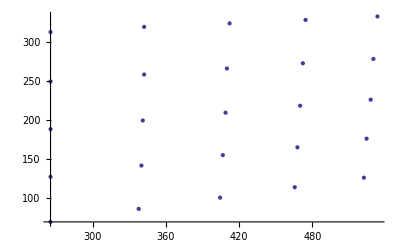

```mathematica
presentedPlot=ListPlot[Flatten[Take[paare,All,-1],1]]
```

#### Plot der Originalpunkte

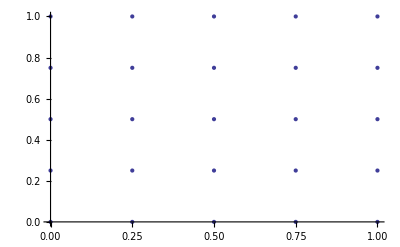

```mathematica
sourcePlot=ListPlot[Flatten[Take[paare,All,1],1]]
```

```mathematica
a1=EuclideanDistance[paare[[1,2]],paare[[21,2]]]/
EuclideanDistance[paare[[1,1]],paare[[21,1]]]//N
b1=EuclideanDistance[paare[[5,2]],paare[[25,2]]]/
EuclideanDistance[paare[[5,1]],paare[[25,1]]]//N
```

243.333

206.964

Teste ein paar Werte (inkl. Stauchung und Offset):

```mathematica
KameraXZuBeamerX[409-265, a1,b1]
```

0.62056

```mathematica
max=BeamerXZuKameraX[0,a1,b1]
BeamerXZuKameraX[.5,a1,b1]/max*(522-265.5)+265.5
```

0.

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
BeamerYZuKameraY[.5,.5,a1,b1,70-126.7]+126.7
paare[[13]]
```

210.924

{{0.5,0.5},{408.889,210.}}

LU: {{0,0},{265.556,70.}}
LL: {{0,1},{265.556,313.333}}
RU: {{1,0},{522.222,126.667}}
RL: {{1,1},{533.333,333.333}}

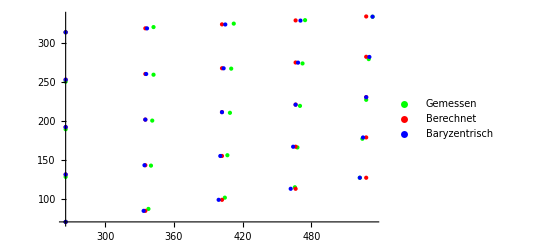

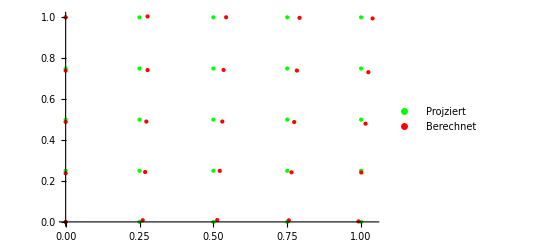

```mathematica
VergleichsPlot[paare,{paare[[1]],paare[[21]],paare[[5]],paare[[25]]}]
```

```mathematica
eckpunkte={cameraResults[[1]],cameraResults[[21]],cameraResults[[5]],cameraResults[[25]]}
```

{{265.556,70.},{265.556,313.333},{527.777,126.667},{527.777,333.631}}

### Determinantengleichungen für Umkehr der viereckigen Baryzentrischen Angleichung

```mathematica
xh=x/.FullSimplify[Solve[Det[
{
(1-x)*{LUx,LUy}+x*{RUx,RUy}-{px,py},
(1-x)*{LLx,LLy}+x*{RLx,RLy}-{px,py}
}
]==0,x]][[2]]
```

(2 LLy LUx-2 LLx LUy-LLy px+LUy px+LLx py-LUx py+LUy RLx-py RLx-LUx RLy+px RLy-LLy RUx+py RUx+LLx RUy-px RUy+√(-4 (LLy (LUx-px)+LUy px-LUx py+LLx (-LUy+py)) ((LLy-RLy) (LUx-RUx)-(LLx-RLx) (LUy-RUy))+(-py RLx+LUy (px+RLx)+px RLy-LUx (py+RLy)+LLy (2 LUx-px-RUx)+py RUx-px RUy+LLx (-2 LUy+py+RUy))^2))/(2 ((LLy-RLy) (LUx-RUx)-(LLx-RLx) (LUy-RUy)))

```mathematica
yh=y/.FullSimplify[Solve[Det[
{
(1-y)*{LUx,LUy}+y*{LLx,LLy}-{px,py},
(1-y)*{RUx,RUy}+y*{RLx,RLy}-{px,py}
}
]==0,y]][[1]]
```

(LLy px-LUy px-LLx py+LUx py-LUy RLx+py RLx+LUx RLy-px RLy-LLy RUx+2 LUy RUx-py RUx+LLx RUy-2 LUx RUy+px RUy+√(-4 ((LLy-LUy) (RLx-RUx)-(LLx-LUx) (RLy-RUy)) (-py RUx+LUy (-px+RUx)+LUx (py-RUy)+px RUy)+(-LLx py+LUx py+py RLx+LUx RLy-px RLy-LUy (px+RLx-2 RUx)+LLy (px-RUx)-py RUx+(LLx-2 LUx+px) RUy)^2))/(2 ((LLy-LUy) (RLx-RUx)-(LLx-LUx) (RLy-RUy)))

#### Test der Determinantengleichungen

```mathematica
LUx=265;LUy=70;
LLx=265;LLy=313;
RUx=522;RUy=126;
RLx=533;RLy=333;
```

```mathematica
px=533;py=333;
xh//N
yh//N
```

1.

1.

In der Mitte schlechter als der Integralansatz, da die perspektivische Verzerrung in der Mitte am Grössten ist.

```mathematica
KameraPixel[{.5,.5}]
```

{396.667,210.833}